```mathematica
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"../src/MultipleScattering2D.wl"];
MemoryInUse[]
```

195482000

```mathematica
Scattered wave from one cylinder;

Scattering in time;
impulse[τ_]= ⅇ^(-5(τ-1)^2);

options=Sequence["Impulse"-> impulse,"ImpulsePeriod"->2.,"PrintChecks"-> False,"Boundary"-> "Neumann","FrequencyModes"->20,"NAngularModes"->4];

data= AcousticScattering[0.5,{0.,2.5},3.0,{4.,.2,.2},options];
(*Usage*)
(*AcousticScattering[radius,sourcePosition,{Subscript[t, 0],Subscript[t, max],δt},{Subscript[R, max],δR,δθ}];*)
(*AcousticScattering[radius,sourcePosition,t,{Subscript[R, max],δR,δθ}]*)

(*Note*)
(*Flatten[data,2]; will produce a list where each element is {t,θ,r,wave[t,θ,r]]}. *)
```

```mathematica
(*And this is how you make a gif!*)
lps=PlotWaves[data];
Export[NotebookDirectory[]<>"WaveS.gif",lps]
```

```mathematica
(*Export and import*)
Export[NotebookDirectory[]<>"WaveS.CSV",data,"CSV"];
```

```mathematica
data=ToExpression[Import[NotebookDirectory[]<>"WaveS.CSV","CSV"]];
```

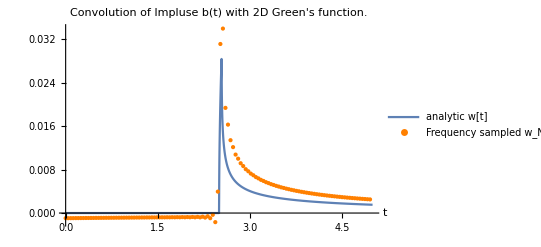

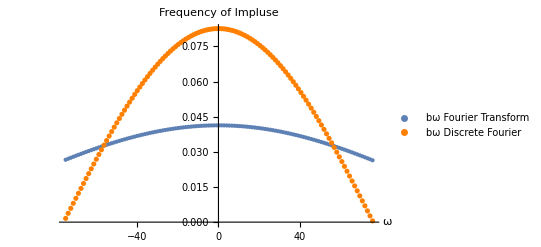

Max Amp: 0.0358686

/home/art/uom/study/Scattering/ScatterCylinder/v2/examples/OneCylinder.gif

```mathematica
In more detail and with scattering coefficients;

(*Scatterer Radius RS, source distance RI and period of incident impulse bT*)
	subN={RS-> .2,RI-> 1.8};T=5; 

(*Set any range for the frequency rngω*)
	NN= 60; δω=2π/(T);δ = δω/4;
	rngω = Range[0, δω NN,δω];
	(*Format needed for discrete Fourier*)
	rngωFourier=  rngω~Join~Reverse@Drop[-rngω,1] +δ;

(*number of angular θ modes *)
	rngn=Range[-2,2]; 
(*Gives the scattering coefficients Subscript[a, n][ω] in list form, where each cylinder scatters ∑_(n=-NN)^NN Subscript[a, n][ω]Subscript[H, n]^(1)[ω r/c] ⅇ^(ⅈ n θ) *)
	scatteringCoefficients=SingleScattererCoefficients[rngωFourier,rngn];

(*Choose the range for the time, radius and angle in cylindrical coordinates*)
	rngr=Range[0.1,2.5,0.2];
	rngθ= Range[0,π+0.1,.1];
         (*To convolute with the source in time*)
	timeImpulse = If[0≤ N[#//Chop,4]≤ T/(2NN+1) ,1,0]&;
	options={"PrintChecks"-> True,"ImpulsePeriod"->2,"Impulse"-> timeImpulse};

(*Calculate and plot the wave field in time*)
	waves= listWaveFromCoefficients[scatteringCoefficients,rngωFourier,rngθ,rngr,options];
	p =PlotWaves[waves];
(*To save a gif!*)
	Export[NotebookDirectory[]<>"OneCylinder.gif",p]
```